# Linear Chiral (E_1=eV_g,E_2=eV_g)(Voltage temperature probe)

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T12uu=TX TY;
T13uu=TX (1-TY);
T21uu=0;
T22uu=(1-TY);
T23uu=TY;
T31uu=TX;
T32uu=TY(1-TX);
T33uu=(1-TX)( 1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=84.8*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(1-T11uu)*G0*df,{G,n0,n1}];
G12=NIntegrate[(-T12uu)*G0*df,{G,n0,n1}];
G13=NIntegrate[(-T13uu)*G0*df,{G,n0,n1}];
G31=NIntegrate[(-T31uu)*G0*df,{G,n0,n1}];
G32=NIntegrate[(-T32uu)*G0*df,{G,n0,n1}];
G33=NIntegrate[(1-T33uu)*G0*df,{G,n0,n1}];
L11=NIntegrate[(1-T11uu)*(G-μ)*L0*df,{G,n0,n1}];
L12=NIntegrate[(-T12uu)*(G-μ)*L0*df,{G,n0,n1}];
L13=NIntegrate[(-T13uu)*(G-μ)*L0*df,{G,n0,n1}];
L23=NIntegrate[(-T23uu)*(G-μ)*L0*df,{G,n0,n1}];
L33=NIntegrate[(1-T33uu)*(G-μ)*L0*df,{G,n0,n1}];
L31=NIntegrate[(-T31uu)*(G-μ)*L0*df,{G,n0,n1}];
L32=NIntegrate[(-T32uu)*(G-μ)*L0*df,{G,n0,n1}];
π11=NIntegrate[(1-T11uu)*(G-μ)*Lp*df,{G,n0,n1}];
π12=NIntegrate[(-T12uu)*(G-μ)*Lp*df,{G,n0,n1}];
π13=NIntegrate[(-T13uu)*(G-μ)*Lp*df,{G,n0,n1}];
π31=NIntegrate[(-T31uu)*(G-μ)*Lp*df,{G,n0,n1}];
π33=NIntegrate[(1-T33uu)*(G-μ)*Lp*df,{G,n0,n1}];
K11=NIntegrate[(1-T11uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K12=NIntegrate[(-T12uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K13=NIntegrate[(-T13uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K31=NIntegrate[(-T31uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K32=NIntegrate[(-T32uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K33=NIntegrate[(1-T33uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z}];
},{x1,0,0.84,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check2.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{30.3978,Null}

check2.dat

# Linear Helical (E_1=eV_g,E_2=eV_g)(Voltage-temperature probe)

```mathematica
kb=1;
T=1;
θ=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=84.8*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z,Jq*h/(kb^2*θ*δT),Subscript[η, r]}]
},{x1,0,0.84,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check4.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{17.424,Null}

check4.dat

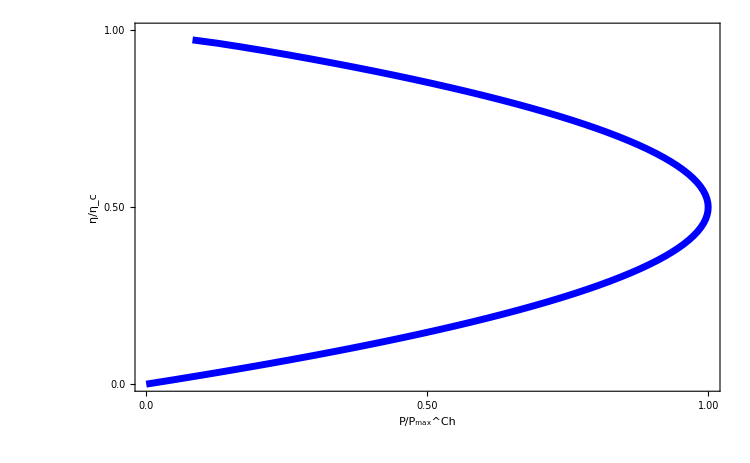

```mathematica
data2=Import["check2.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data2},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^Ch",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750]
```

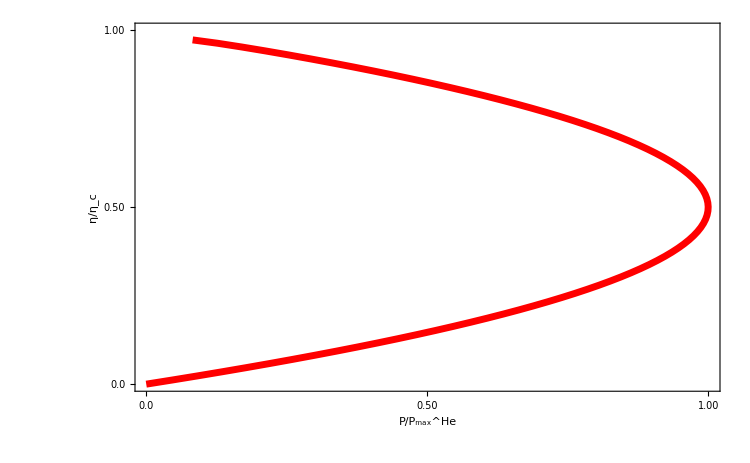

```mathematica
data4=Import["check4.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^He",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750]
```

# Non-linear chiral (E_1=eV_g,E_2=eV_g)(Voltage-temperature probe)

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=3.7;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=(2ec)/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,T3,P/(2*0.316493),2*η}];
},{Vg,-1,20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check122.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.05252×10^-20 and 2.19433×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.05252×10^-20 and 2.19433×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.76747×10^-13 and 1.97659×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.34224×10^-17 and 7.80795×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.51956×10^-16 and 1.94517×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.50389×10^-16 and 5.79789×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.7036×10^-17 and 7.23721×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.1672×10^-16 and 2.68432×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.65382×10^-16 and 7.21809×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.90908×10^-17 and 3.63336×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.27364×10^-16 and 1.65443×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.26674×10^-17 and 7.50736×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.08544×10^-17 and 2.16605×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.19646×10^-16 and 1.21941×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.2602×10^-13 and 1.29256×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.57527×10^-19 and 1.13071×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.35663×10^-18 and 5.92694×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.75428×10^-17 and 7.02383×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.51328×10^-18 and 3.10565×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.83411×10^-17 and 2.15215×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.5918×10^-18 and 3.02192×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.32549×10^-18 and 1.54627×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.4663×10^-17 and 1.12637×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2294×10^-18 and 1.52289×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03255×10^-17 and 5.36767×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.1164×10^-17 and 3.46561×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.57485×10^-18 and 7.69184×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.72908×10^-19 and 3.11143×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.61647×10^-18 and 2.44866×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.1122×10^-19 and 3.16429×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.88176×10^-14 and 2.3185×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.57179×10^-13 and 1.95234×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.54511×10^-19 and 1.49468×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03346×10^-14 and 7.42324×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.63104×10^-14 and 5.62076×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.37514×10^-14 and 3.78627×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.13531×10^-15 and 2.45091×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.87123×10^-15 and 2.23939×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.75278×10^-15 and 2.92807×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.77542×10^-16 and 1.26133×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2586×10^-15 and 1.18274×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.78534×10^-15 and 1.17226×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{1177.95,Null}

```mathematica
"check122.dat"
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

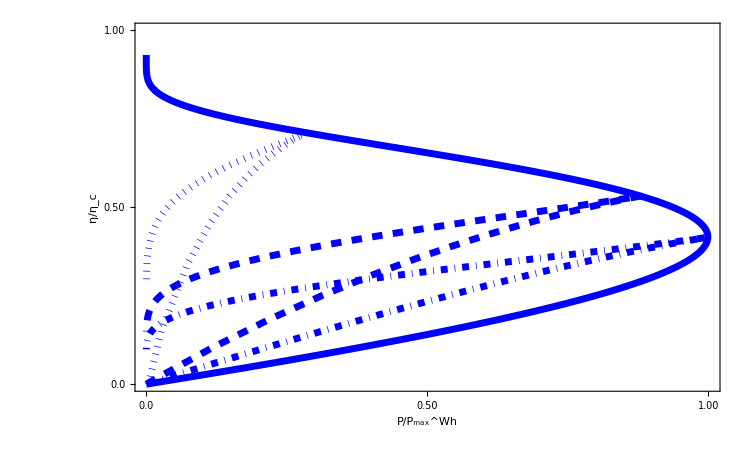

```mathematica
data1=Import["check120.dat"][[All,{4,5}]];
data2=Import["check121.dat"][[All,{4,5}]];
data3=Import["check122.dat"][[All,{4,5}]];
data4=Import["check12.dat"][[All,{4,5}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue,DotDashed],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Blue,Dotted],Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

# Non-linear helical (E_1=eV_g,E_2=eV_g)(Voltage-temperature probe)

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=3.7;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,T3,P/(2*0.316493),2*η}];
},{Vg,-1,20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check142.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.91935×10^-13 and 2.62259×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.3633×10^-13 and 1.74909×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.03491×10^-13 and 7.74262×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.92202×10^-13 and 5.68935×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.29213×10^-13 and 2.45133×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.64426×10^-13 and 1.63287×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.26565×10^-14 and 1.2444×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.44128×10^-13 and 3.71532×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.54117×10^-15 and 1.25091×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.96268×10^-15 and 7.06562×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.32707×10^-14 and 2.66406×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.71924×10^-15 and 7.59724×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.62381×10^-16 and 4.41608×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.54366×10^-15 and 1.97464×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.79551×10^-16 and 4.0831×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.80292×10^-16 and 1.74191×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.31735×10^-15 and 8.46066×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.8708×10^-16 and 1.50196×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.93732×10^-17 and 3.88504×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.37992×10^-16 and 2.56305×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.1525×10^-17 and 4.03478×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.13312×10^-17 and 3.61128×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.02859×10^-16 and 2.46254×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.78363×10^-17 and 3.22806×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.2313×10^-18 and 1.51581×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.19101×10^-17 and 1.1649×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.65171×10^-18 and 8.82976×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.07976×10^-19 and 8.40008×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.14508×10^-18 and 6.4644×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.57689×10^-18 and 7.28676×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.72722×10^-15 and 1.54219×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.26144×10^-14 and 1.33733×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.82277×10^-14 and 6.19262×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.31678×10^-18 and 3.37×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.24366×10^-17 and 2.84504×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.89183×10^-19 and 1.19694×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.61833×10^-15 and 7.23383×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.14865×10^-15 and 5.37917×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.25567×10^-15 and 5.68755×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.08863×10^-16 and 1.20465×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.72758×10^-16 and 1.17584×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.7355×10^-16 and 2.89972×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.06156×10^-17 and 1.31899×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.91949×10^-17 and 1.1672×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.16112×10^-17 and 1.19539×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{1385.17,Null}

check14.dat

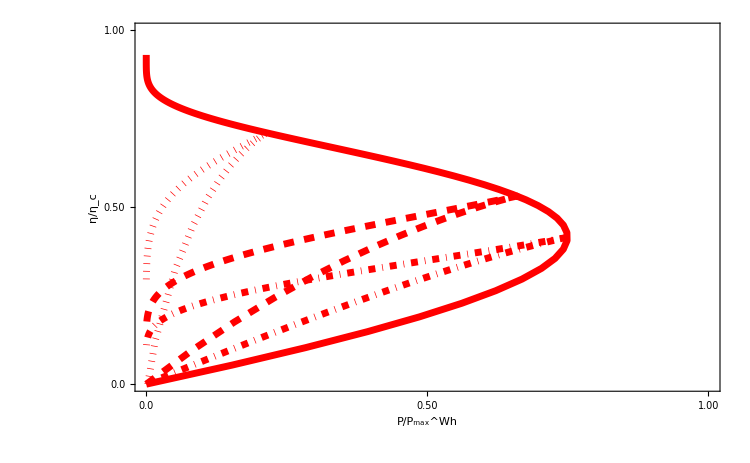

```mathematica
data1=Import["check140.dat"][[All,{4,5}]];
data2=Import["check141.dat"][[All,{4,5}]];
data3=Import["check142.dat"][[All,{4,5}]];
data4=Import["check143.dat"][[All,{4,5}]];
Needs["PlotLegends`"]
A3=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red,DotDashed],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Red,Dotted],Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,35],LabelStyle->Directive[Bold,Black,35]]
```

# Linear chiral refrigerator (E_1=eV_g,E_2=eV_g)(Voltage-temperature probe)

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T12uu=TX TY;
T13uu=TX (1-TY);
T21uu=0;
T22uu=(1-TY);
T23uu=TY;
T31uu=TX;
T32uu=TY(1-TX);
T33uu=(1-TX)( 1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=84.8*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(1-T11uu)*G0*df,{G,n0,n1}];
G12=NIntegrate[(-T12uu)*G0*df,{G,n0,n1}];
G13=NIntegrate[(-T13uu)*G0*df,{G,n0,n1}];
G31=NIntegrate[(-T31uu)*G0*df,{G,n0,n1}];
G32=NIntegrate[(-T32uu)*G0*df,{G,n0,n1}];
G33=NIntegrate[(1-T33uu)*G0*df,{G,n0,n1}];
L11=NIntegrate[(1-T11uu)*(G-μ)*L0*df,{G,n0,n1}];
L12=NIntegrate[(-T12uu)*(G-μ)*L0*df,{G,n0,n1}];
L13=NIntegrate[(-T13uu)*(G-μ)*L0*df,{G,n0,n1}];
L23=NIntegrate[(-T23uu)*(G-μ)*L0*df,{G,n0,n1}];
L33=NIntegrate[(1-T33uu)*(G-μ)*L0*df,{G,n0,n1}];
L31=NIntegrate[(-T31uu)*(G-μ)*L0*df,{G,n0,n1}];
L32=NIntegrate[(-T32uu)*(G-μ)*L0*df,{G,n0,n1}];
π11=NIntegrate[(1-T11uu)*(G-μ)*Lp*df,{G,n0,n1}];
π12=NIntegrate[(-T12uu)*(G-μ)*Lp*df,{G,n0,n1}];
π13=NIntegrate[(-T13uu)*(G-μ)*Lp*df,{G,n0,n1}];
π31=NIntegrate[(-T31uu)*(G-μ)*Lp*df,{G,n0,n1}];
π33=NIntegrate[(1-T33uu)*(G-μ)*Lp*df,{G,n0,n1}];
K11=NIntegrate[(1-T11uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K12=NIntegrate[(-T12uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K13=NIntegrate[(-T13uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K31=NIntegrate[(-T31uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K32=NIntegrate[(-T32uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K33=NIntegrate[(1-T33uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
ηr1=J1/P1*0.01;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z,-J1/Jq,ηr1}];
},{x1,0.84,8,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check50.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{214.808,Null}

check50.dat

# Linear helical refrigerator (E_1=V_g,E_2=2 V_g)(voltage probe)

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
θ=1;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=1.5*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=2ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11-(G13*(G31))/(G33);
LeT=L11-(G13*L31)/G33;
LhV=π11-(π13*G31)/G33;
LhT=K11-(π13*L31)/G33;
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
P=(LeT)^2/(4*Gc)*(δT)^2;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
ηr1=J1/P1*0.01;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,Jq*h/(kb^2*θ*δT),Subscript[η, r],-J1*h/(kb^2*θ*δT)/0.67,-J1/Jq,ηr1}]
},{x1,0.020,10,0.001}];//AbsoluteTiming
list=Sort[list1];
Export["check30.dat",list]
```

{643.862,Null}

check30.dat

# Linear helical refrigerator (E_1=V_g,E_2=2 V_g)(voltage-temperature probe)

```mathematica
kb=1;
T=1;
θ=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=84.80*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
ηr1=J1/P1*0.01;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,Jq*h/(kb^2*θ*δT),Subscript[η, r],-J1*h/(kb^2*θ*δT)/(2.15*10^-7),-J1/Jq,ηr1}]
},{x1,0.84,8,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check40.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.46367×10^-37 and 5.84433×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.49186×10^-37 and 5.01011×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{73.3347,Null}

check40.dat

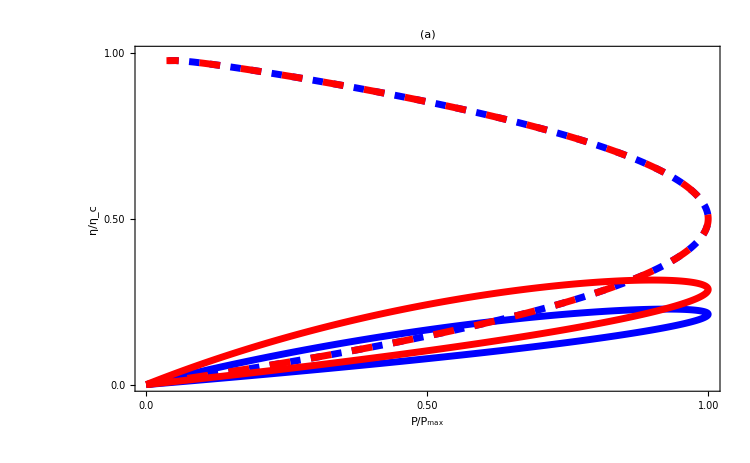

```mathematica
data1=Import["check1.dat"][[All,{4,5}]];
data2=Import["check2.dat"][[All,{3,4}]];
data3=Import["check3.dat"][[All,{3,4}]];
data4=Import["check4.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

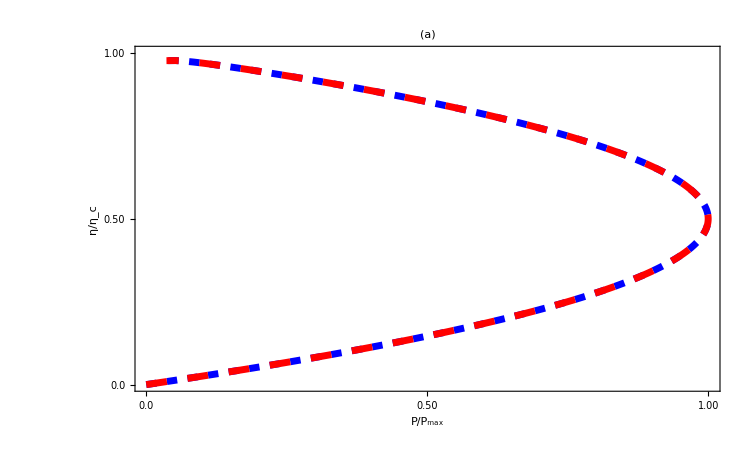

```mathematica
data2=Import["check2.dat"][[All,{3,4}]];
data4=Import["check4.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data2,data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

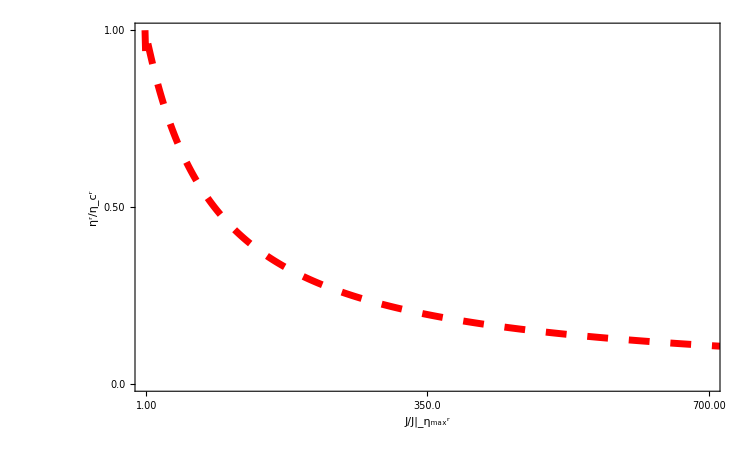

```mathematica
data2=Import["check40.dat"][[All,{5,6}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{1.00001,700},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0001,"1.00"},{350,"350.0"},{700,"700.00"}},None}},FrameLabel->{Style["J/J|_(η_max^r)",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750]
```

```mathematica
data2=Import["check50.dat"][[All,{10,11}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{1.00001,700},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0001,"1.00"},{350,"350.0"},{700,"700.00"}},None}},FrameLabel->{Style["J/J|_(η_max^r)",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

-Graphics-

```mathematica
GraphicsGrid[{{A2}},ImageSize->1500]
```

-Graphics-

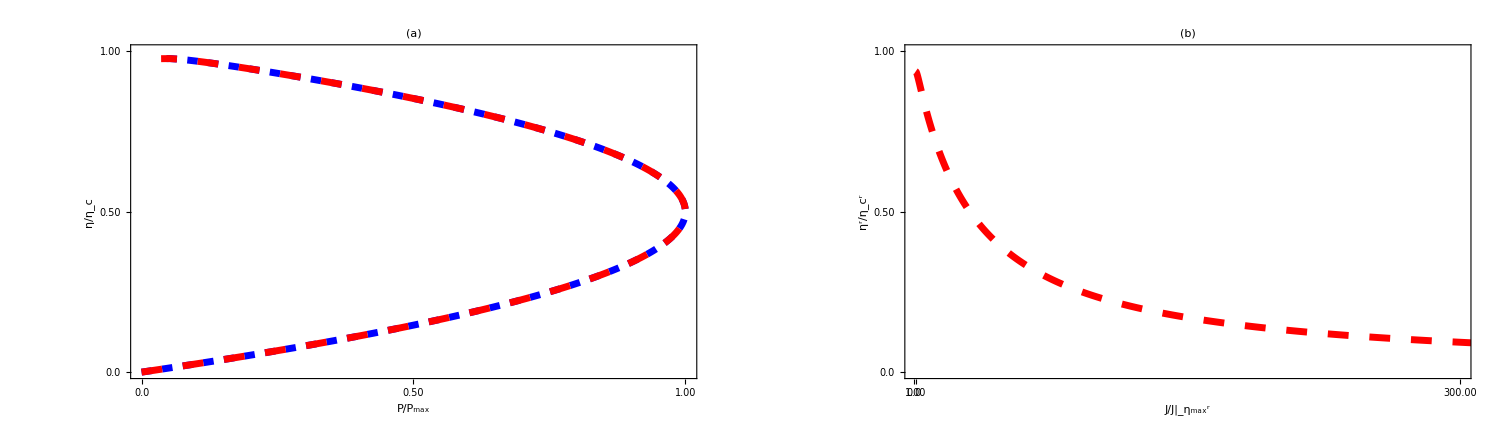

```mathematica
A5=GraphicsGrid[{{A1,A2}},ImageSize->1500]
```

```mathematica
A5=Legended[GraphicsGrid[{{A1,A2}},ImageSize->1500],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5],Dashed],Directive[Red,AbsoluteThickness[5],Dashed]},{Style["Chiral",Bold,Black,35],Style["Helical",Bold,Black,35]},LegendFunction->Framed,LegendLayout->"Row"],{0.5,0.0}]]
```

-Graphics-

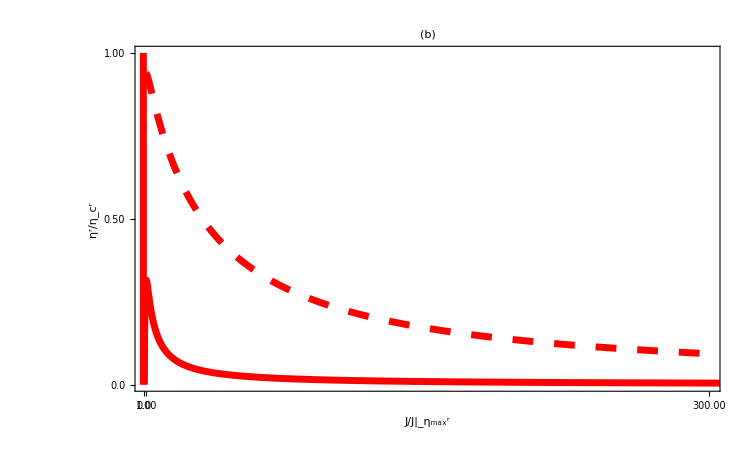

```mathematica
A5=Legended[GraphicsGrid[{{A2}},ImageSize->1500],Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5],Dashed]},{Style["VP",Bold,Black,35],Style["VTP",Bold,Black,35]},LegendFunction->Framed,LegendLayout->"Row"],{0.5,0.5}]]
```

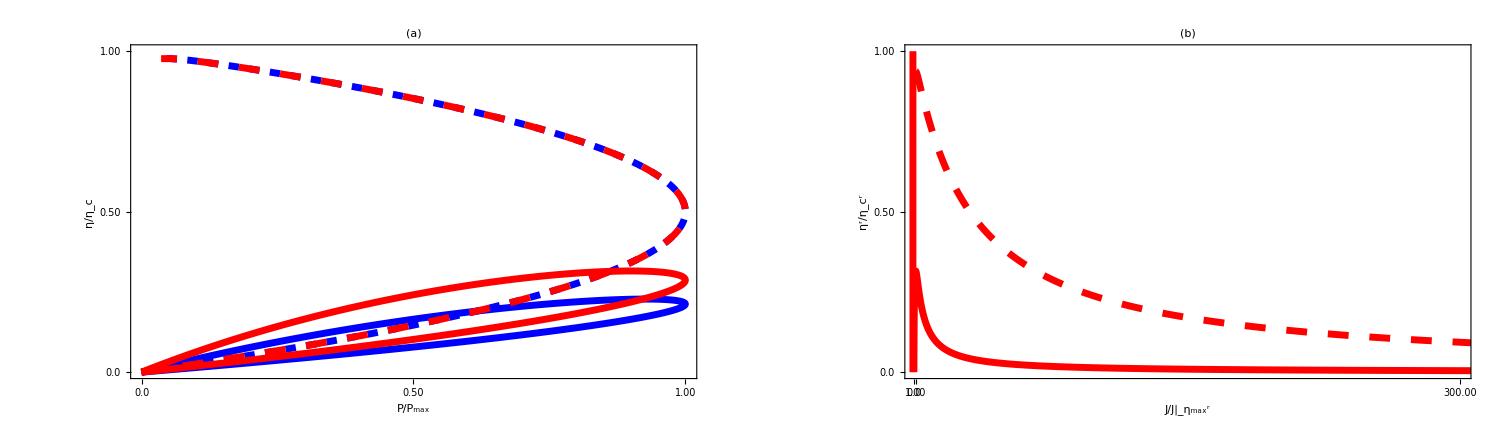

```mathematica
A5=Legended[GraphicsGrid[{{A1,A2}},ImageSize->1500],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5],Dashed],Directive[Red,AbsoluteThickness[5],Dashed]},{Style["Chiral(VP)",Bold,Black,35],Style["Helical(VP)",Bold,Black,35],Style["Chiral(VTP)",Bold,Black,35],Style["Helical(VTP)",Bold,Black,35]},LegendFunction->Framed,LegendLayout->"Row"],{0.5,0.0}]]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig3.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig3.pdf

```mathematica
kb=1.38*10^(-23);
T=0.1;
θ=0.1;
h=6.634*10^(-34);
ec=1.6*10^(-19);
μ=0;
hb=1.05*10^(-34);
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=5.20*a/ec;
V=x1*a/ec;
E2=2ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=μ-0.1*ae;
n1=μ+0.1*ae;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1))
```

0.93994

```mathematica
V=LhT/LhV(1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))*0.01
```

9.68342×10^-6

```mathematica
(ec*V)/a
```

1.12271

```mathematica
V=x1*a/ec;
x1=1.1227;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
ηr1=J1/(V*I1)*0.1
```

0.93994

```mathematica
kb=1.38*10^(-23);
T=0.1;
h=6.634*10^(-34);
ec=1.6*10^(-19);
μ=0;
θ=0.1;
hb=1.05*10^(-34);
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=0.8*a/ec;
V=x1*a/ec;
E2=2ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=μ-0.1*ae;
n1=μ+0.1*ae;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11-(G13*(G31))/(G33);
LeT=L11-(G13*L31)/G33;
LhV=π11-(π13*G31)/G33;
LhT=K11-(π13*L31)/G33;
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*10;
P=(LeT)^2/(4*Gc)*(δT)^2;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1))
```

0.283339

```mathematica
V=LhT/LhV(1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))*0.01
```

4.47361×10^-6

```mathematica
(ec*V)/a
```

0.51868

```mathematica
(J1/(V*I1)*0.1)/.{x1->0.51868}
```

0.283339

# Nonlinear chiral refrigerator (E_1=V_g,E_2=2 V_g)(voltage probe)

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=20+Vg/5;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GaussKronrodRule",MaxRecursion->1000,AccuracyGoal->20];
I4=FindRoot[{I3[V3]==0},{{V3,Vg}}];
V3=V3/.I4[[1]];
I1=2/h NIntegrate[(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G)(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=J1/(V*I1);
list=AppendTo[list1,{Vg,V3,J1/(2*0.82),η}];
},{Vg,0,6.90,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check50.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.84892×10^-18 and 3.99535×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.06496×10^-13 and 1.27348×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.06496×10^-13 and 1.27348×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{24.0008,Null}

check50.dat

# Nonlinear chiral refrigerator (E_1=V_g,E_2=2 V_g)(voltage-temperature probe)

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=20+Vg/5;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=(2*ec)/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
ηr=J1/P;
list=AppendTo[list1,{Vg,P/(2*0.316493),-J1/(2*0.82),ηr}];
},{Vg,0.0,10.20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check60.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.91181×10^-17 and 1.26329×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.49765×10^-17 and 5.24575×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.98458×10^-14 and 8.37995×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.90326×10^-16 and 1.18794×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.55426×10^-15 and 1.13104×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{196.295,Null}

check60.dat

# Nonlinear helical refrigerator (E_1=V_g,E_2=2 V_g)(voltage probe)

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=20+Vg/5;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GaussKronrodRule",MaxRecursion->1000,AccuracyGoal->20];
I4=FindRoot[{I3[V3]==0},{{V3,Vg}}];
V3=V3/.I4[[1]];
I1=1/h NIntegrate[(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G)(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=J1/(V*I1);
list=AppendTo[list1,{Vg,V3,J1/(2*0.82),η}];
},{Vg,0,6.60,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check70.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.72966×10^-17 and 9.26658×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.29373×10^-12 and 2.21049×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.29373×10^-12 and 2.21049×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.0571×10^-17 and 2.09756×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.97973×10^-17 and 2.34448×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.6782×10^-15 and 1.83367×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.37879×10^-14 and 6.02798×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.37879×10^-14 and 6.02798×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.17901×10^-17 and 6.53403×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.17901×10^-17 and 6.53403×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.55176×10^-18 and 4.50847×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.63149×10^-18 and 8.07157×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.76083×10^-19 and 2.38482×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.09482×10^-17 and 3.68653×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.6248×10^-19 and 1.93508×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.09482×10^-17 and 3.68653×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.24937×10^-20 and 3.85258×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.96261×10^-18 and 1.25435×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.32934×10^-20 and 1.07756×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{25.714,Null}

check70.dat

# Nonlinear helical refrigerator (E_1=V_g,E_2=2 V_g)(voltage-temperature probe)

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=20+Vg/5;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GaussKronrodRule",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}}];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=1/h NIntegrate[(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G)(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=J1/(V*I1);
list=AppendTo[list1,{Vg,V3,J1/(2*0.82),η}];
},{Vg,0,10.20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check80.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.72747×10^-15 and 1.29216×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.32596×10^-16 and 7.5083×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.66336×10^-15 and 2.14988×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.97178×10^-15 and 2.55341×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.72747×10^-15 and 1.29216×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.32596×10^-16 and 7.5083×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.42686×10^-13 and 1.30578×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.54342×10^-12 and 5.79954×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.42686×10^-13 and 1.30578×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.3016×10^-14 and 8.07563×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.19553×10^-13 and 5.91148×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.3016×10^-14 and 8.07563×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.37612×10^-18 and 8.51631×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.37612×10^-18 and 8.51631×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.09802×10^-19 and 6.65384×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.15788×10^-20 and 1.23075×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{98.6814,Null}

check80.dat

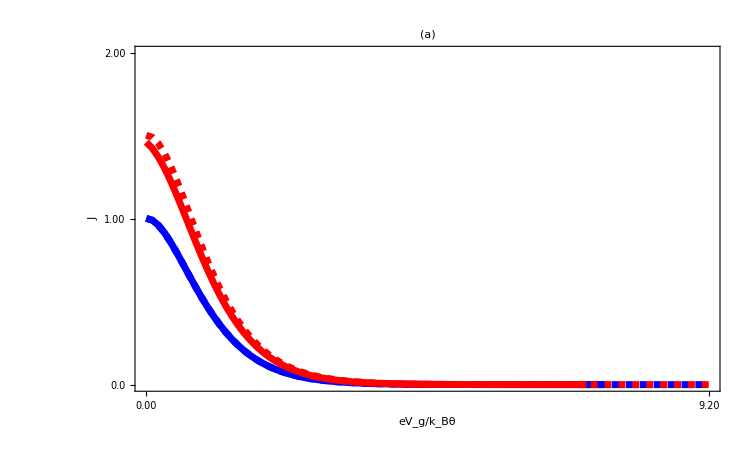

```mathematica
data1=Import["check50.dat"][[All,{1,3}]];
data2=Import["check60.dat"][[All,{1,3}]];
data3=Import["check70.dat"][[All,{1,3}]];
data4=Import["check80.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0,9.20},{0,2}},Frame->True,FrameTicks->{{{{0,"0.0"},{1,"1.00"},{2,"2.00"}},None},{{{0,"0.00"},{9.20,"9.20"}},None}},FrameLabel->{Style["eV_g/k_Bθ",45,Bold,Black],Style["J",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,Dashed]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

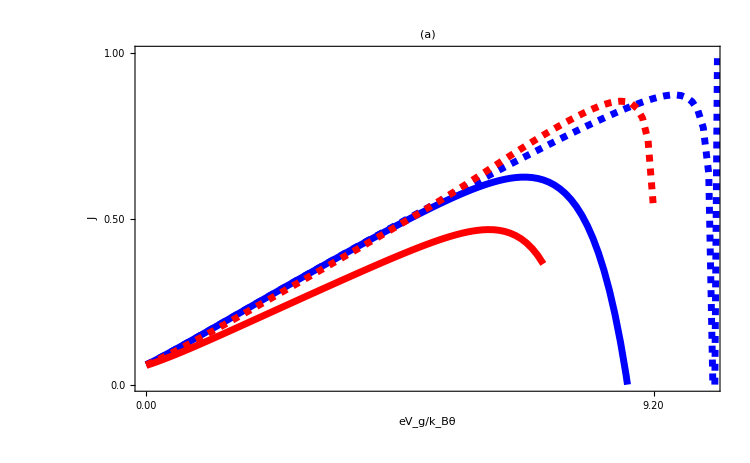

```mathematica
data1=Import["check50.dat"][[All,{1,4}]];
data2=Import["check60.dat"][[All,{1,4}]];
data3=Import["check70.dat"][[All,{1,4}]];
data4=Import["check80.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0,10.20},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{0,"0.00"},{9.20,"9.20"}},None}},FrameLabel->{Style["eV_g/k_Bθ",45,Bold,Black],Style["J",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,Dashed]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

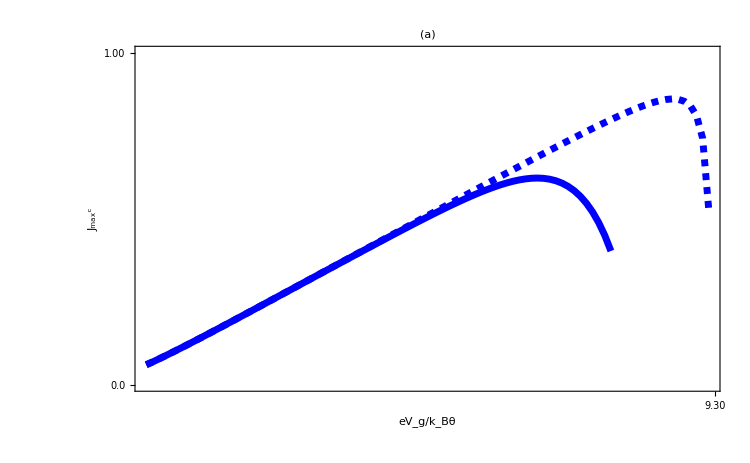

```mathematica
data1=Import["check50.dat"][[All,{1,4}]];
data2=Import["check60.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{0,9.20},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{1,"1.00"},{2,"2.00"}},None},{{{-1,"-1.00"},{9.30,"9.30"}},None}},FrameLabel->{Style["eV_g/k_Bθ",45,Bold,Black],Style["J_max^c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,Dashed]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

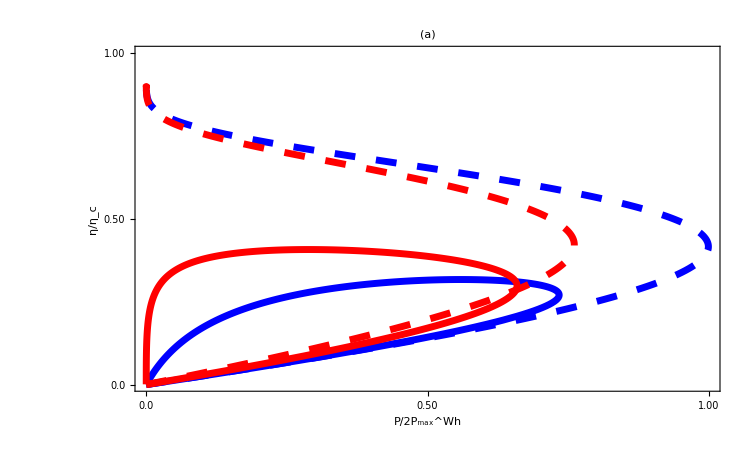

```mathematica
data1=Import["check11.dat"][[All,{3,4}]];
data2=Import["check12.dat"][[All,{4,5}]];
data3=Import["check13.dat"][[All,{3,4}]];
data4=Import["check14.dat"][[All,{4,5}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,1},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{0.50,"0.50"}},None}},FrameLabel->{Style["P/2P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[15]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

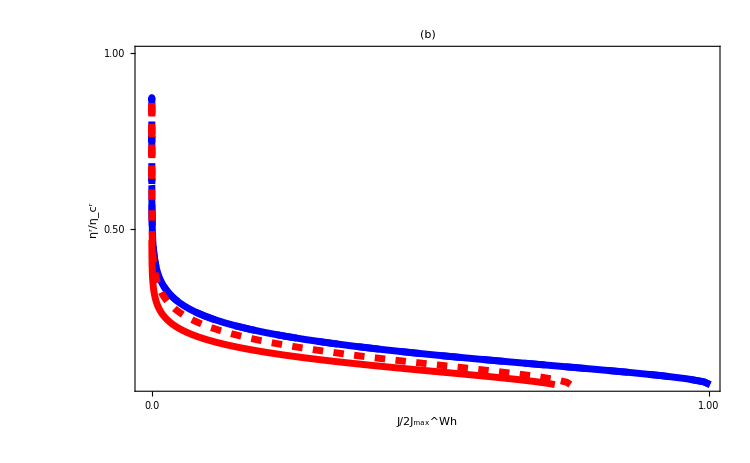

```mathematica
data1=Import["check50.dat"][[All,{3,4}]];
data2=Import["check60.dat"][[All,{3,4}]];
data3=Import["check70.dat"][[All,{3,4}]];
data4=Import["check80.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{-0.01,1},{0.06,1}},Frame->True,FrameTicks->{{{{-0.01,"0.0"},{1,"1.00"},{0.50,"0.50"}},None},{{{0,"0.0"},{1,"1.00"},{2,"2.00"}},None}},FrameLabel->{Style["J/2J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[15]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[7.5]]},ImageSize->750,PlotLabel->Style["(b)"],LabelStyle->Directive[Bold,Black,35]]
```

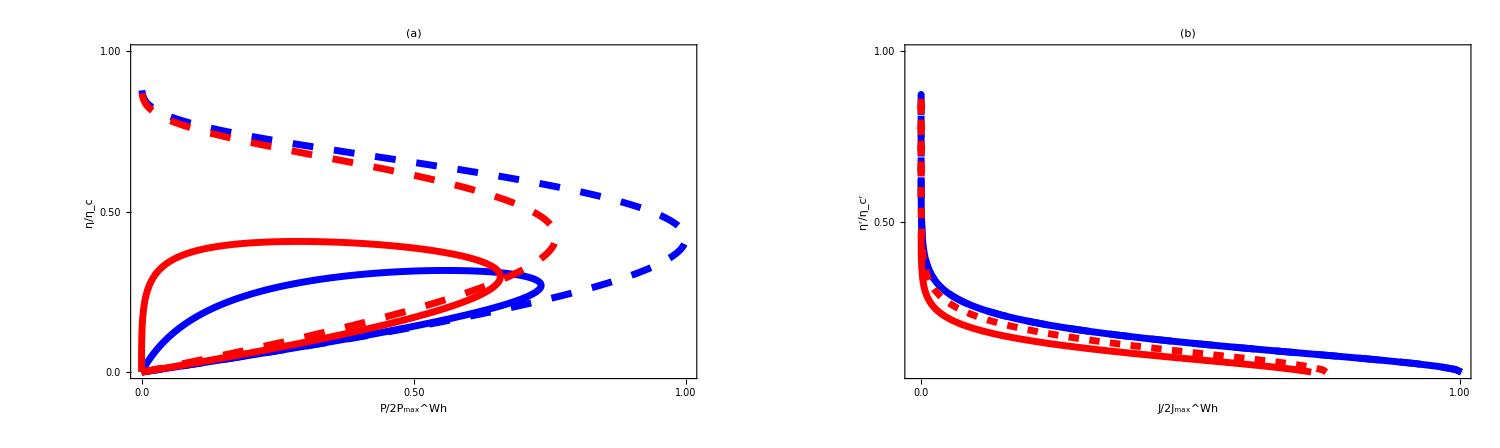

```mathematica
A5=Legended[GraphicsGrid[{{A1,A2}},ImageSize->1500],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5],Dashed],Directive[Red,AbsoluteThickness[5],Dashed]},{Style["Chiral(VP)",Bold,Black,35],Style["Helical(VP)",Bold,Black,35],Style["Chiral(VTP)",Bold,Black,35],Style["Helical(VTP)",Bold,Black,35]},LegendFunction->Framed,LegendLayout->"Row"],{0.5,0.0}]]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig4.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig4.pdf

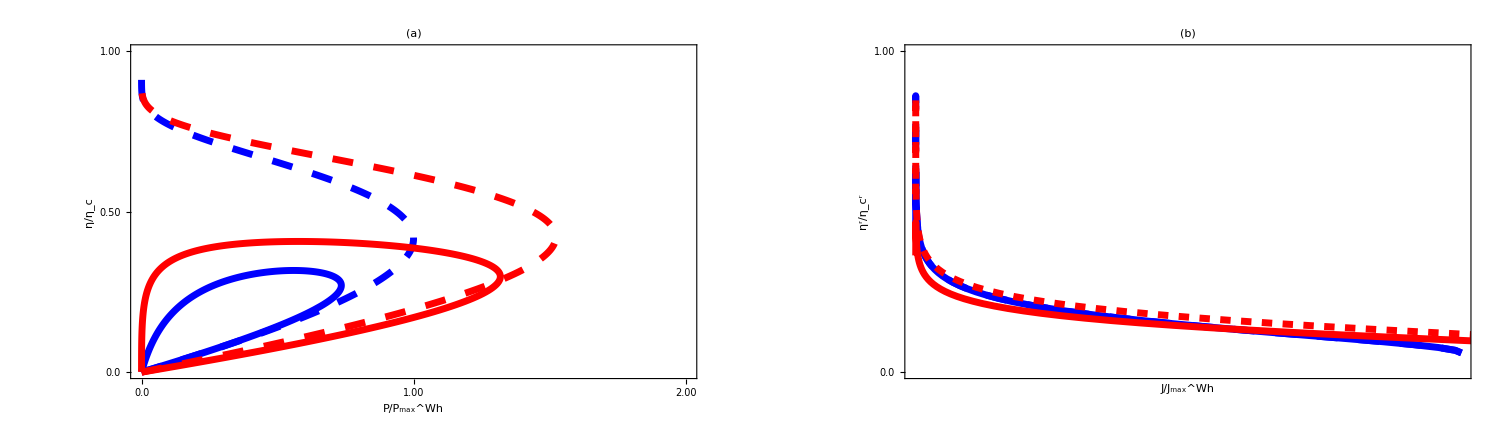

```mathematica
A5=Legended[GraphicsGrid[{{A1,A2}},ImageSize->1500],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5],Dashed],Directive[Red,AbsoluteThickness[5],Dashed]},{"Chiral(VP)","Helical(VP)","Chiral(VTP)","Helical(VTP)"},LegendFunction->Framed,LegendLayout->"Row"],{0.5,0.0}]]
```

```mathematica
A5=Legended[GraphicsGrid[{{A1,A2}},ImageSize->1500],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5],Dashed],Directive[Red,AbsoluteThickness[5],Dashed]},{Style["Chiral(VP)",Bold,Black,35],Style["Helical(VP)",Bold,Black,35],Style["Chiral(VTP)",Bold,Black,35],Style["Helical(VTP)",Bold,Black,35]},LegendFunction->(Framed[Style[#,20]]&),LegendLayout->"Row"],{0.5,0.0}]]
```

-Graphics-

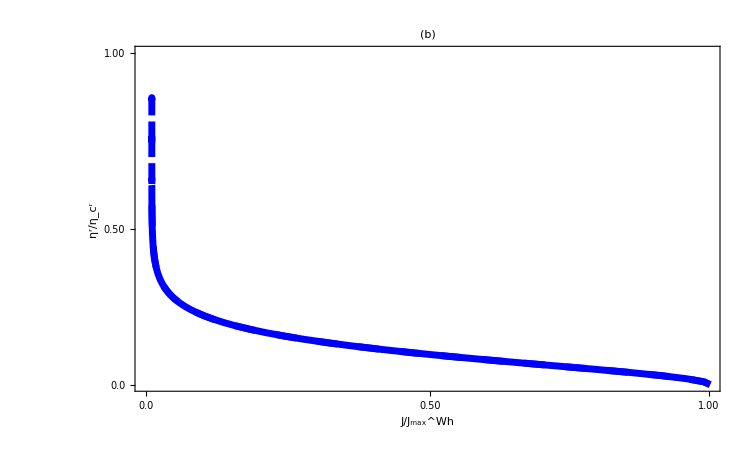

```mathematica
data1=Import["check50.dat"][[All,{3,4}]];
data2=Import["check60.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{-0.01,1},{0.06,1}},Frame->True,FrameTicks->{{{{0.06,"0.0"},{1,"1.00"},{0.50,"0.50"}},None},{{{-0.01,"0.0"},{1,"1.00"},{0.50,"0.50"}},None}},FrameLabel->{Style["J/J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(b)"],LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
A5=Legended[GraphicsGrid[{{A2}},ImageSize->1500],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5],Dashed]},{Style["VP",Bold,Black,35],Style["VTP",Bold,Black,35]},LegendFunction->Framed,LegendLayout->"Row"],{0.5,0.5}]]
```

-Graphics-

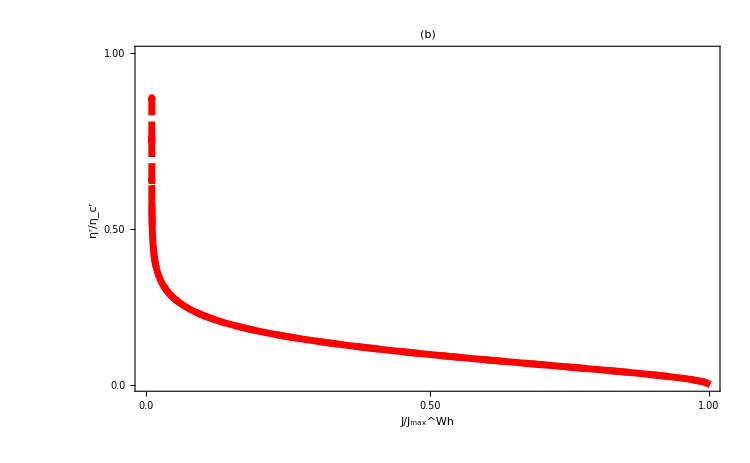

```mathematica
data1=Import["check50.dat"][[All,{3,4}]];
data2=Import["check60.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{-0.01,1},{0.06,1}},Frame->True,FrameTicks->{{{{0.06,"0.0"},{1,"1.00"},{0.50,"0.50"}},None},{{{-0.01,"0.0"},{1,"1.00"},{0.50,"0.50"}},None}},FrameLabel->{Style["J/J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(b)"],LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
A5=Legended[GraphicsGrid[{{A2}},ImageSize->1500],Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5],Dashed]},{Style["VP",Bold,Black,35],Style["VTP",Bold,Black,35]},LegendFunction->Framed,LegendLayout->"Row"],{0.5,0.5}]]
```

-Graphics-

```mathematica
T31=TX;
T32=TY (1-TX);
T12=TX*TY;
T13=TX (1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2 π (G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2 π (G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=2;
T2=1;
T3=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=Vg;
SetSharedVariable[list1]
list1={};
ParallelDo[{E1=Vg;
E2=Vg;
I1=ec/h NIntegrate[(T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V) (T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,P/(0.316493),2*η}];},{Vg,0,30,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check111.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{38.7554,Null}

check111.dat

```mathematica
T31=TX;
T32=TY (1-TX);
T12=TX*TY;
T13=TX (1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2 π (G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2 π (G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=2;
T2=1;
T3=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=(Vg+1)/2;
SetSharedVariable[list1]
list1={};
ParallelDo[{E1=Vg;
E2=Vg;
I1=ec/h NIntegrate[(T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V) (T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,P/(0.316493),2*η}];},{Vg,0,30,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check112.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{41.3645,Null}

check112.dat

```mathematica
T31=TX;
T32=TY (1-TX);
T12=TX*TY;
T13=TX (1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2 π (G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2 π (G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=2;
T2=1;
T3=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=(Vg+3)/4;
SetSharedVariable[list1]
list1={};
ParallelDo[{E1=Vg;
E2=Vg;
I1=ec/h NIntegrate[(T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V) (T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,P/(0.316493),2*η}];},{Vg,-10,30,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check113.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{48.0836,Null}

check113.dat

```mathematica
T31=TX;
T32=TY (1-TX);
T12=TX*TY;
T13=TX (1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2 π (G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2 π (G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=2;
T2=1;
T3=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=(Vg+10)/15;
SetSharedVariable[list1]
list1={};
ParallelDo[{E1=Vg;
E2=Vg;
I1=ec/h NIntegrate[(T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V) (T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,P/(0.316493),2*η}];},{Vg,-10,30,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check114.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{54.8338,Null}

check114.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

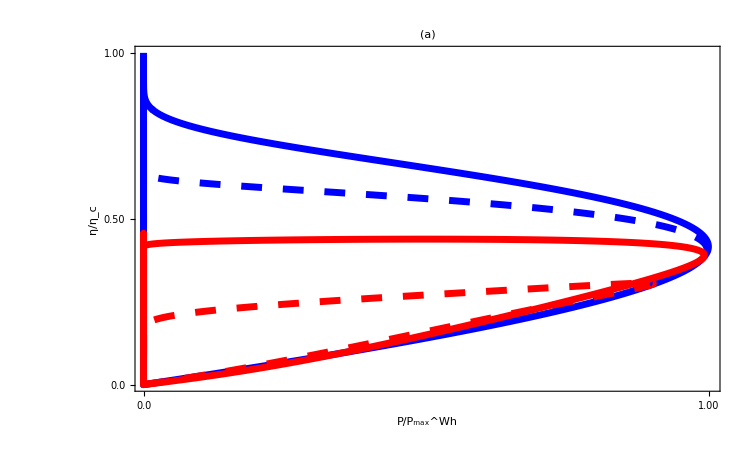

```mathematica
data1=Import["check111.dat"][[All,{2,3}]];
data2=Import["check112.dat"][[All,{2,3}]];
data3=Import["check113.dat"][[All,{2,3}]];
data4=Import["check114.dat"][[All,{2,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0048,1},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{2,"2.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[15]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=2*Vg;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,P/(0.316493),2*η}];
},{Vg,0,10,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check13.dat",list]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

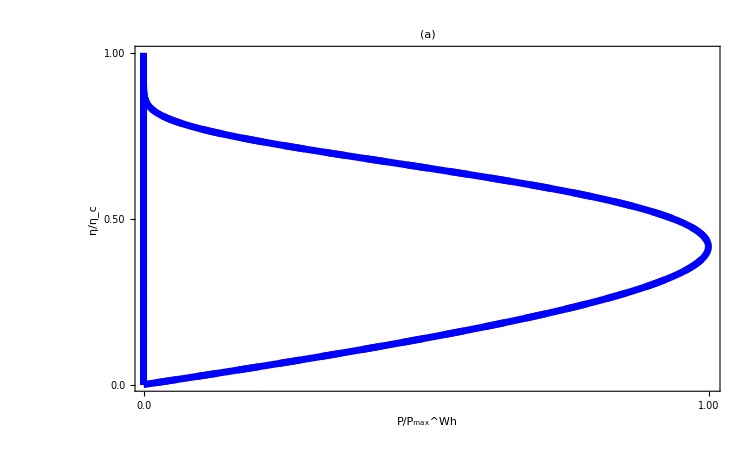

```mathematica
data1=Import["check111.dat"][[All,{2,3}]];
data2=Import["check112.dat"][[All,{2,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{0.0048,1},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{2,"2.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[15]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

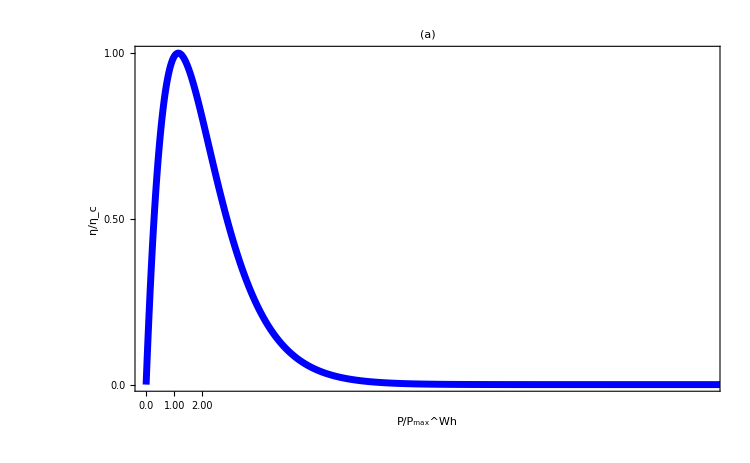

```mathematica
data1=Import["check111.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1},Frame->True,PlotRange->{{0.0048,20},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{2,"2.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[15]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

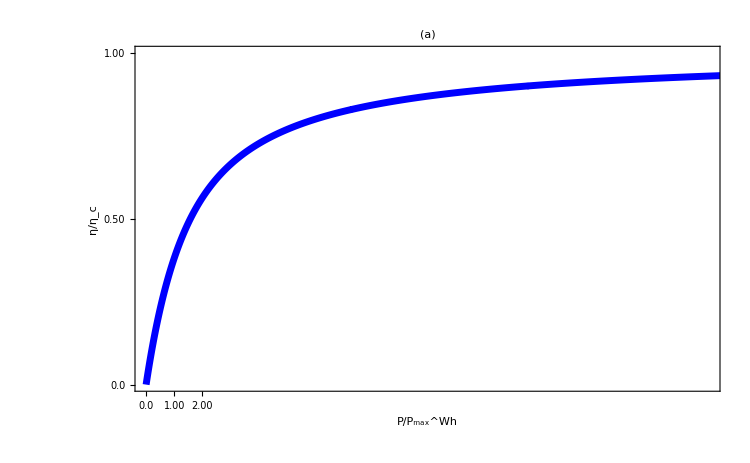

```mathematica
data1=Import["check111.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1},Frame->True,PlotRange->{{0.0048,20},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{2,"2.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[15]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
E1=Vg
```

Vg

```mathematica
E2=2Vg
```

2 Vg

```mathematica
TX
```

1/(1+ⅇ^(-62.8319 (G-Vg)))

```mathematica
TY
```

1/(1+ⅇ^(-62.8319 (G-2 Vg)))

```mathematica
T12
```

1/((1+ⅇ^(-62.8319 (G-2 Vg))) (1+ⅇ^(-62.8319 (G-Vg))))

```mathematica
T13
```

(1-1/(1+ⅇ^(-62.8319 (G-2 Vg))))/(1+ⅇ^(-62.8319 (G-Vg)))

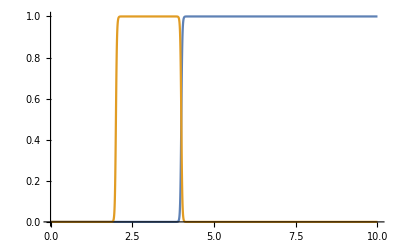

```mathematica
Plot[{T12/.{Vg->2},T13/.{Vg->2}},{G,0,10}]
```

```mathematica
f1
```

1/(1+ⅇ^((G+Vg)/2))

```mathematica
f2
```

1/(1+ⅇ^G)

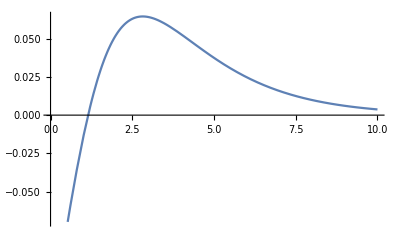

```mathematica
Plot[(f1-f2)/.{Vg->1.15},{G,0,10}]
```

```mathematica
T31=TX;
T32=TY (1-TX);
T12=TX*TY;
T13=TX (1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2 π (G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2 π (G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=2;
T2=1;
T3=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=Vg+0.01;
SetSharedVariable[list1]
list1={};
ParallelDo[{E1=Vg;
E2=2Vg;
I1=ec/h NIntegrate[(T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V) (T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,P/(0.316493),2*η}];},{Vg,0,30,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check110.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{41.3211,Null}

check110.dat

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=Vg;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,P/(2*0.316493),2*η}];
},{Vg,0,30,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check111.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{40.9194,Null}

check111.dat

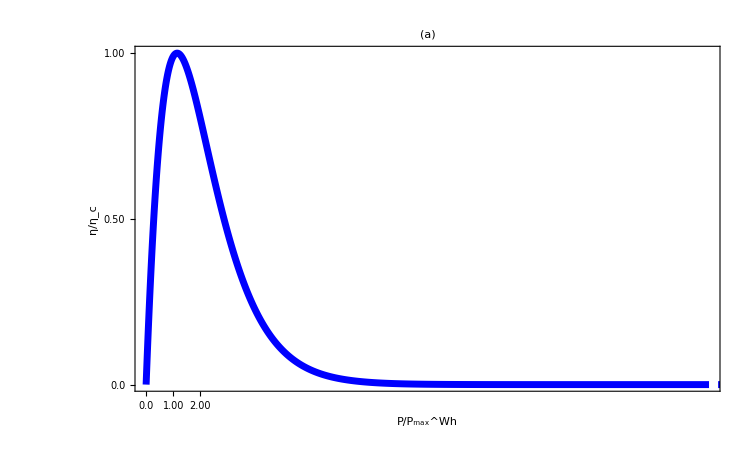

```mathematica
data1=Import["check110.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1},Frame->True,PlotRange->{{0.0048,20.75},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{2,"2.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[15]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
data1=Import["check110.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1},Frame->True,PlotRange->{{0.0048,20},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{2,"2.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[15]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[15]]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

-Graphics-

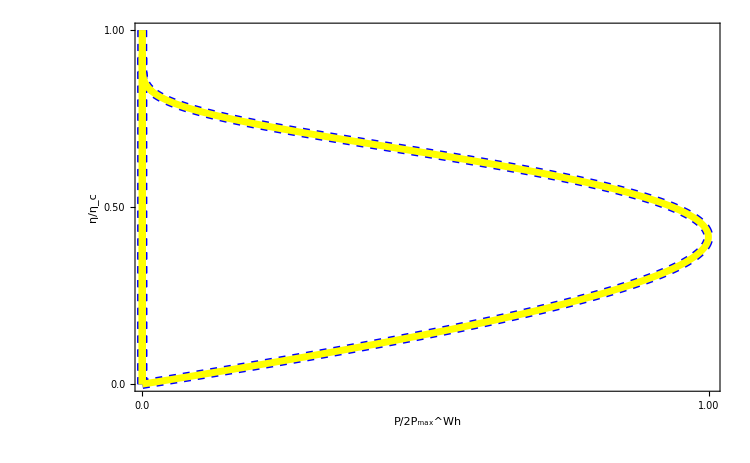

```mathematica
data1=Import["check110.dat"][[All,{2,3}]];
data2=Import["check111.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{0.007,1},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{2,"2.00"}},None}},FrameLabel->{Style["P/2P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[7],Opacity[1],Blue,AbsoluteDashing[5]],Directive[AbsoluteThickness[5],Opacity[1],Yellow]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

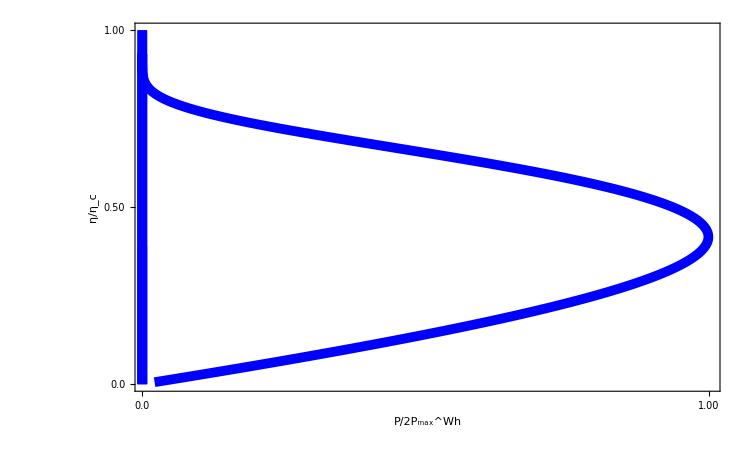

```mathematica
data1=Import["check110.dat"][[All,{2,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1},Frame->True,PlotRange->{{0.007,1},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{2,"2.00"}},None}},FrameLabel->{Style["P/2P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[7],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Yellow]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

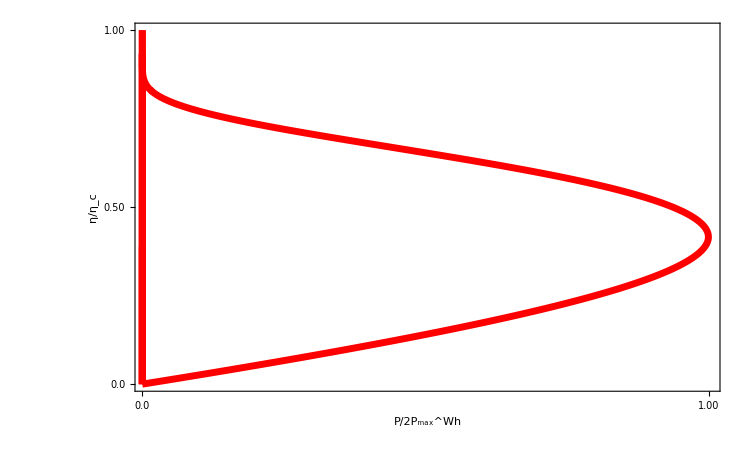

```mathematica
data1=Import["check111.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1},Frame->True,PlotRange->{{0.007,1},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{2,"2.00"}},None}},FrameLabel->{Style["P/2P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
A5=Legended[GraphicsGrid[{{A1}},ImageSize->1500],Placed[LineLegend[{Directive[Yellow,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5],Dashed]},{Style["Chiral",Bold,Black,35],Style["Helical",Bold,Black,35]},LegendFunction->Framed,LegendLayout->"Row"],{0.5,-0.1}]]
```

-Graphics-

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig100supple.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig100supple.pdf

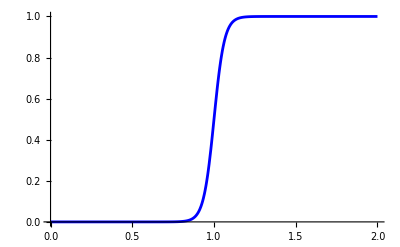

```mathematica
Plot[1/(1+Exp[-2π(G-1)/0.2]),{G,0,2},Ticks->None,PlotStyle->{Directive[AbsoluteThickness[2],Opacity[1],Blue]}]
```

```mathematica
T31=TX;
T32=TY (1-TX);
T12=TX*TY;
T13=TX (1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2 π (G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2 π (G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=2;
T2=1;
T3=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=Vg-1;
SetSharedVariable[list1]
list1={};
ParallelDo[{E1=Vg;
E2=2Vg;
I1=ec/h NIntegrate[(T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V) (T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,P/(0.316493),2*η}];},{Vg,0,30,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check112.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{43.4117,Null}

check112.dat

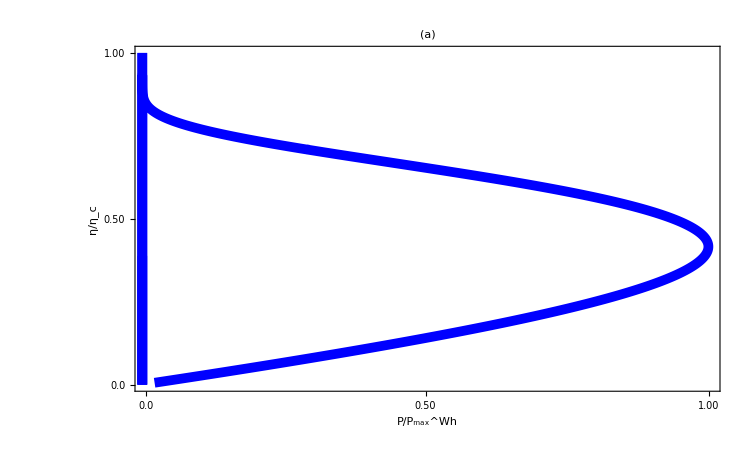

```mathematica
data1=Import["check110.dat"][[All,{2,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1},Frame->True,PlotRange->{{0.007,1},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0.007,"0.0"},{0.50,"0.50"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[7],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Yellow]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
T31=TX;
T32=TY (1-TX);
T12=TX*TY;
T13=TX (1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2 π (G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2 π (G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=1+θ;
T2=1;
T3=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
θ=-Vg;
V=1.1;
SetSharedVariable[list1]
list1={};
ParallelDo[{E1=Vg;
E2=2Vg;
I1=ec/h NIntegrate[(T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V) (T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,P/(0.316493),2*η}];},{Vg,1,30,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check113.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-1/(1+ⅇ^G)+1/(1+ⅇ^(Plus[«2»] Power[«2»])))/((1+ⅇ^(-62.8319 (Times[«2»]+G))) (1+ⅇ^(-62.8319 (Times[«2»]+G))))+((1-1/(1+ⅇ^Times[«2»])) (-1/(1+ⅇ^G)+1/(1+ⅇ^(Plus[«2»] Power[«2»]))))/(1+ⅇ^(-62.8319 (Times[«2»]+G))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate::inumr: The integrand ((-1/(1+Power[«2»])+1/(1+ⅇ^Times[«2»]))/((1+ⅇ^(-62.8319 Plus[«2»])) (1+ⅇ^(-62.8319 Plus[«2»])))+((1-1/(1+Power[«2»])) (-1/(1+Power[«2»])+1/(1+ⅇ^Times[«2»])))/(1+ⅇ^(-62.8319 Plus[«2»]))) (1.1+G) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
T31=TX;
T32=TY (1-TX);
T12=TX*TY;
T13=TX (1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2 π (G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2 π (G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=2;
T2=1;
T3=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=Vg+1;
SetSharedVariable[list1]
list1={};
ParallelDo[{E1=1+Vg;
E2=1+2Vg;
I1=ec/h NIntegrate[(T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V) (T12 (f1-f2)+T13 (f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,P/(0.316493),2*η}];},{Vg,-20,20,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check210.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{54.6743,Null}

check210.dat

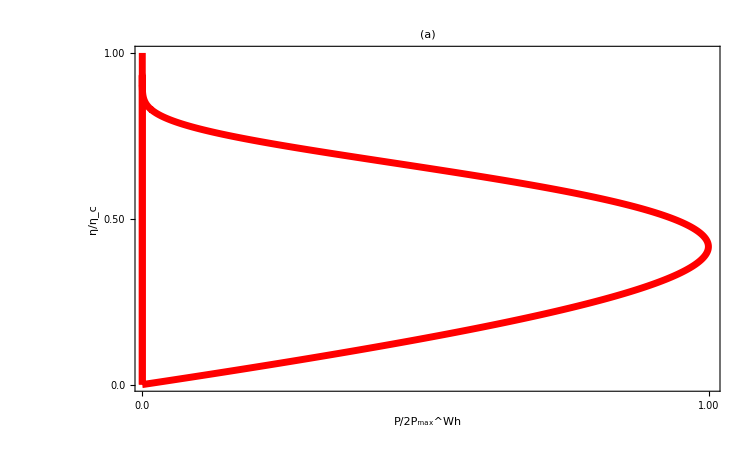

```mathematica
data1=Import["check210.dat"][[All,{2,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1},Frame->True,PlotRange->{{0.007,1},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{2,"2.00"}},None}},FrameLabel->{Style["P/2P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
T31=TX;
T32=TY (1-TX);
T12=TX*TY;
T13=TX (1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2 π (G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2 π (G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=2;
T2=1;
T3=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=20+Vg/5;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
ηr=J1/P;
list=AppendTo[list1,{Vg,-J1/0.82,ηr}];
},{Vg,0.0,20.5,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check160.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{9.42513,Null}

check160.dat

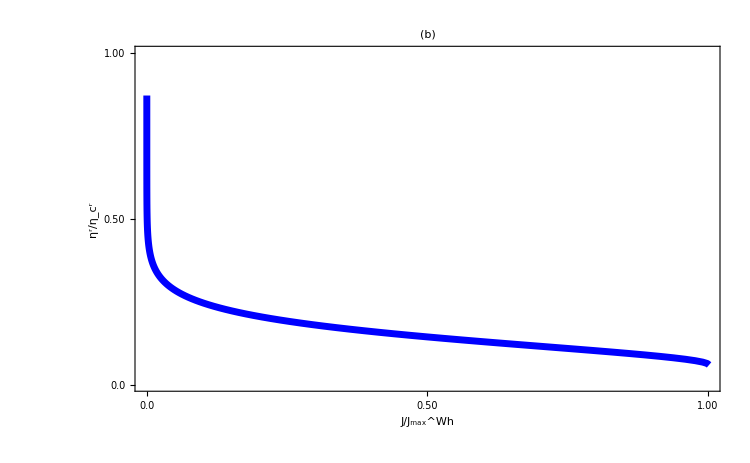

```mathematica
data2=Import["check160.dat"][[All,{2,3}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{-0.001,1.002},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{0.5,"0.50"}},None}},FrameLabel->{Style["J/J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750,PlotLabel->Style["(b)"],LabelStyle->Directive[Bold,Black,35]]
```

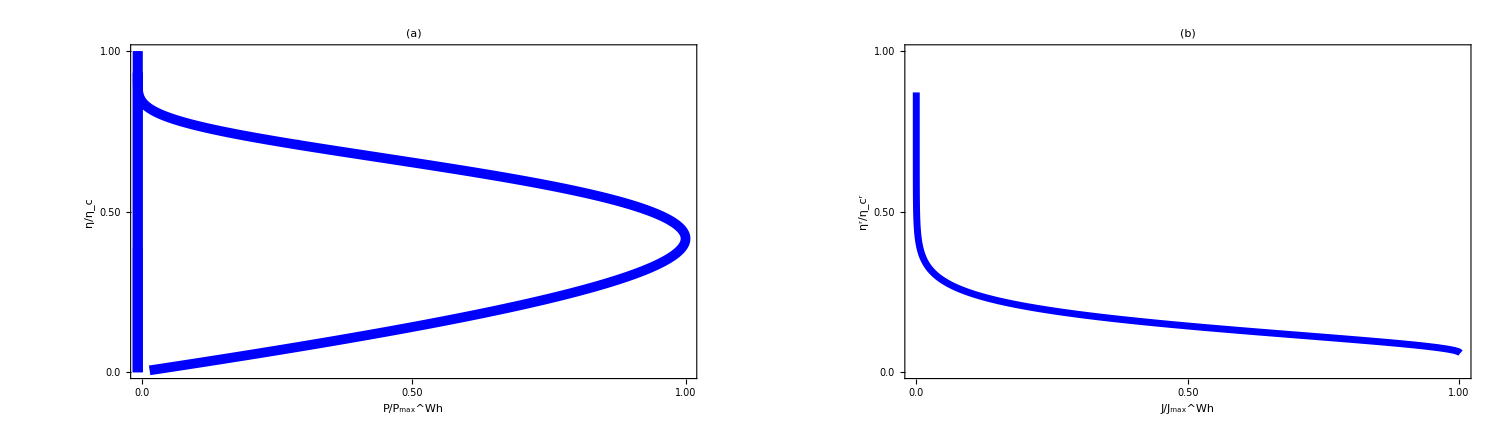

```mathematica
A5=GraphicsGrid[{{A1,A2}},ImageSize->1500]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig3supple.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig3supple.pdf

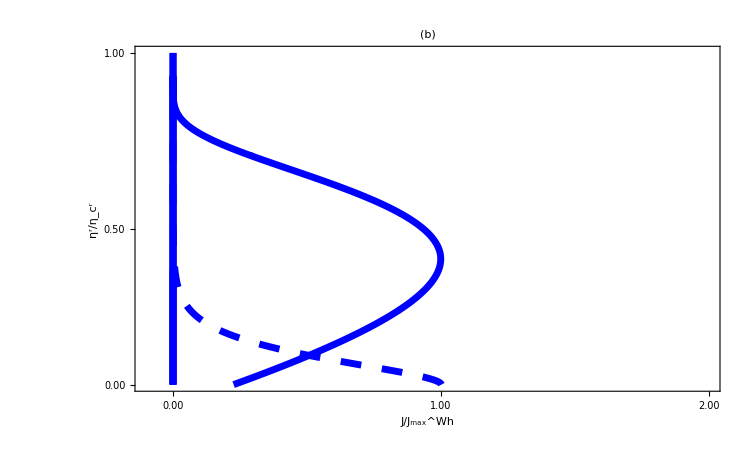

```mathematica
data1=Import["check110.dat"][[All,{2,3}]];
data2=Import["check160.dat"][[All,{2,3}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{-0.1,2},{0.06,1}},Frame->True,FrameTicks->{{{{0.06,"0.00"},{1,"1.00"},{0.50,"0.50"}},None},{{{0,"0.00"},{1,"1.00"},{2,"2.00"}},None}},FrameLabel->{Style["J/J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[15]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[7.5]]},ImageSize->750,PlotLabel->Style["(b)"],LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2 π (G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2 π (G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=2;
T2=1;
T3=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=20;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
ηr=J1/P;
list=AppendTo[list1,{Vg,-J1/(2*0.82),ηr}];
},{Vg,0.0,20.5,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check161.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{9.71398,Null}

check161.dat

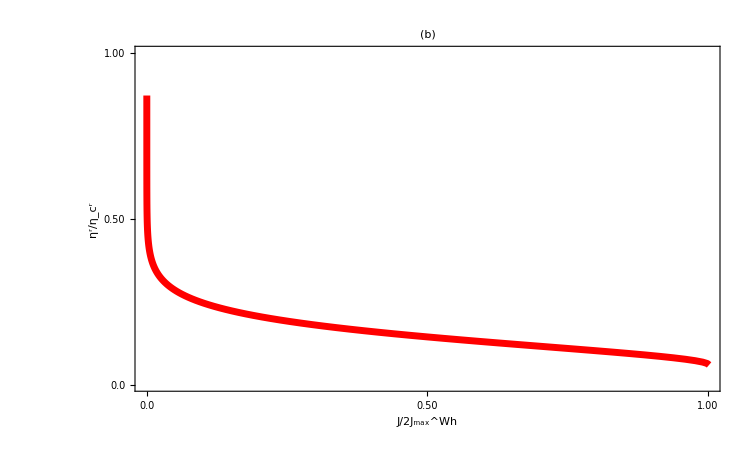

```mathematica
data1=Import["check161.dat"][[All,{2,3}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data1},Frame->True,PlotRange->{{-0.001,1.002},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{0.5,"0.50"}},None}},FrameLabel->{Style["J/2J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,PlotLabel->Style["(b)"],LabelStyle->Directive[Bold,Black,35]]
```

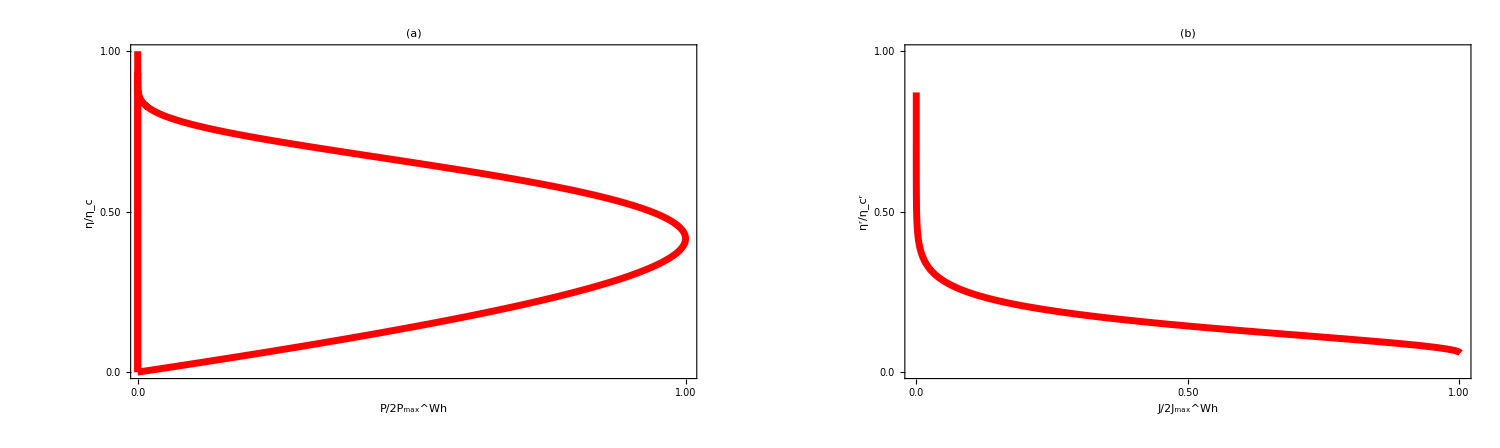

```mathematica
A5=GraphicsGrid[{{A1,A2}},ImageSize->1500]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig4supple.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig4supple.pdf

```mathematica
T31=TX;
T32=TY (1-TX);
T12=TX;
T13=TX (1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2 π (G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2 π (G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=2;
T2=1;
T3=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=Vg;
SetSharedVariable[list1]
list1={};
ParallelDo[{E1=Vg;
E1=Vg;
I1=2ec/h NIntegrate[(T12 (f1-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G+V) (T12 (f1-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,P/(2*0.316493),2*η}];},{Vg,0,30,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check212.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{37.3769,Null}

check212.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

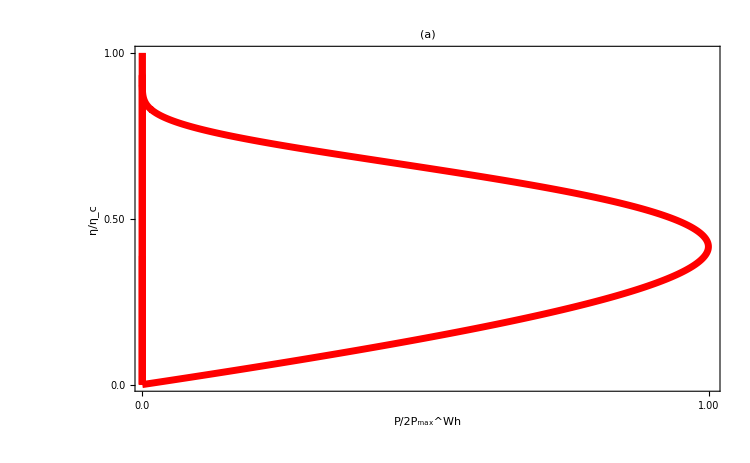

```mathematica
data1=Import["check212.dat"][[All,{2,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1},Frame->True,PlotRange->{{0.007,1},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{2,"2.00"}},None}},FrameLabel->{Style["P/2P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
T12=TX;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2 π (G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2 π (G-E2)/(hb*ω)]);
V1=-V;
V2=0;
V3=0;
T1=2;
T2=1;
T3=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
SetSharedVariable[list1]
list1={};
ParallelDo[{
For[V=1,V<=50,V=V+1,
{E1=5+Vg;
I1=ec/h NIntegrate[(T12(f1-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G)(T12(f1-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
ηr=J1/P;
list=AppendTo[list1,{V,Vg,-J1/0.82,ηr}];
}];
},{Vg,-10.0,10,1}];//AbsoluteTiming
list=Sort[list1];
Export["check170.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{16.7195,Null}

check170.dat

```mathematica
NIntegrate[G*(1/(1+Exp[G/1])),{G,0,∞}]
```

0.822467

General::munfl: Exp[-1256.6] is too small to represent as a normalized machine number; precision may be lost.

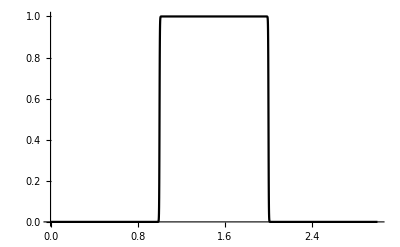

```mathematica
Plot[1/(1+Exp[-2π(G-1)/0.01])1/(1+Exp[2π(G-2)/0.01]),{G,0,3},Ticks->None,PlotStyle->Black,AxesStyle->Directive[Black,12,Thick]]
```

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=3.7;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=(2ec)/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,T3,P/(2*0.316493),2*η}];
},{Vg,-1,20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check122.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.26919×10^-12 and 1.80501×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.00344×10^-12 and 2.45512×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.22404×10^-12 and 1.10419×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.40671×10^-17 and 4.53679×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.24748×10^-16 and 2.11076×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.33565×10^-16 and 4.47234×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.97292×10^-17 and 5.48691×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.77189×10^-16 and 4.51141×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.4609×10^-17 and 1.22059×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.66134×10^-16 and 7.65939×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.66759×10^-13 and 1.5144×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.67937×10^-17 and 2.72573×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.03256×10^-18 and 4.11136×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.00253×10^-16 and 4.12855×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.0483×10^-13 and 6.61812×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.06137×10^-18 and 1.51319×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.06002×10^-17 and 1.70845×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.1142×10^-13 and 1.8265×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.05176×10^-19 and 9.43714×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.14266×10^-18 and 1.2802×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.84347×10^-18 and 5.68054×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.61625×10^-19 and 2.97299×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.08393×10^-17 and 4.52527×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.79222×10^-14 and 2.16682×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.71238×10^-18 and 1.71851×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.94009×10^-17 and 1.75673×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.8193×10^-17 and 1.53521×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.95704×10^-17 and 7.04473×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.9781×10^-17 and 6.91515×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.7309×10^-17 and 1.0719×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{356.65,Null}

check122.dat

```mathematica
data1=Import["check120.dat"][[All,{4,5}]];
data2=Import["check121.dat"][[All,{4,5}]];
data3=Import["check122.dat"][[All,{4,5}]];
data4=Import["check12.dat"][[All,{4,5}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue,DotDashed],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Blue,Dotted],Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

-Graphics-

```mathematica
Export["/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(a).pdf",A1,ImageResolution->300]
```

/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(a).pdf

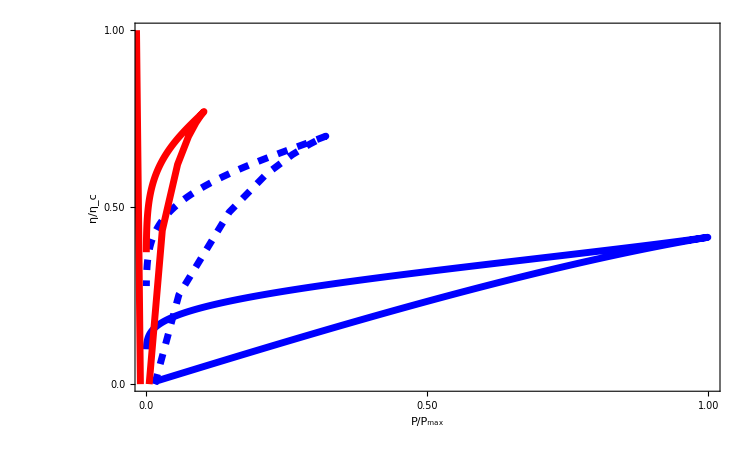

```mathematica
data1=Import["check120.dat"][[All,{4,5}]];
data2=Import["check121.dat"][[All,{4,5}]];
data3=Import["check122.dat"][[All,{4,5}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Purple]},ImageSize->750,LabelStyle->Directive[Bold,Black,35],PlotLabel->Style["(a)"],LabelStyle->Directive[Bold,Black,35]]
```

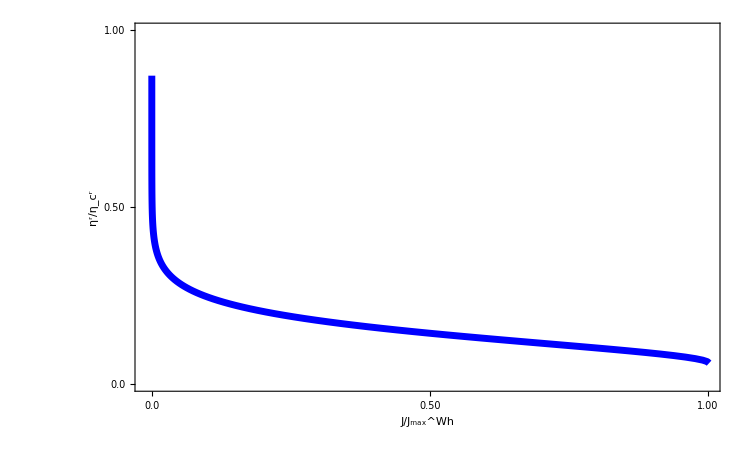

```mathematica
data1=Import["check161.dat"][[All,{2,3}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data1},Frame->True,PlotRange->{{-0.01,1.002},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0,"1.00"},{0,"0.0"},{0.5,"0.50"}},None}},FrameLabel->{Style["J/J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(b).pdf",A2,ImageResolution->300]
```

/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(b).pdf

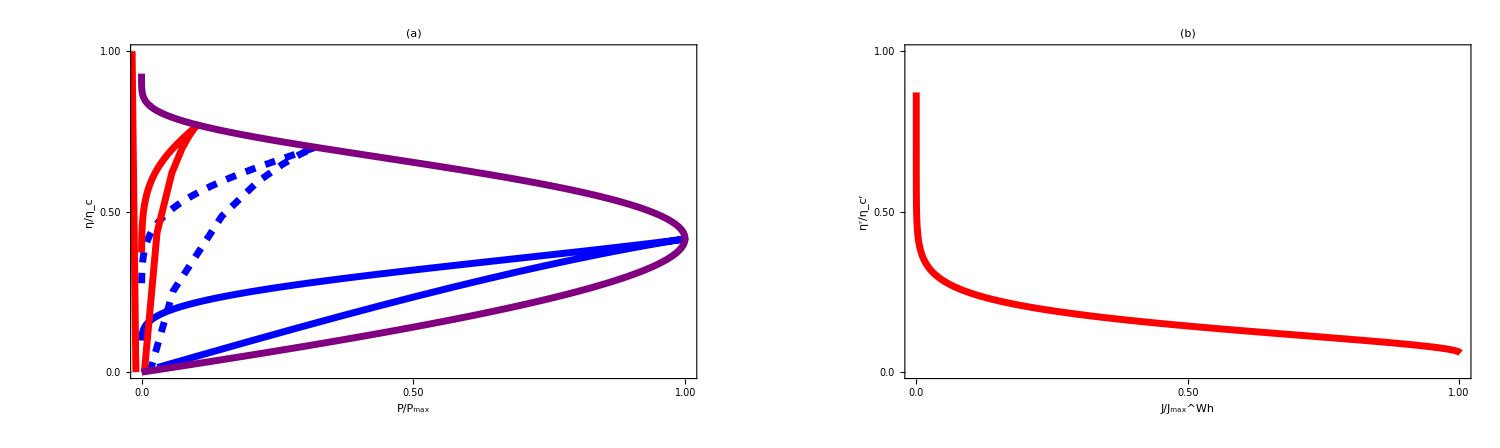

```mathematica
A5=GraphicsGrid[{{A1,A2}},ImageSize->1500]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig4.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig4.pdf

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=Vg;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,T3,P/(2*0.316493),2*η}];
},{Vg,0,20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check143.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.91935×10^-13 and 2.62259×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.75279×10^-12 and 1.08651×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.03491×10^-13 and 7.74262×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.06462×10^-11 and 4.41715×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.16836×10^-12 and 2.96373×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.10459×10^-13 and 1.06768×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.56133×10^-12 and 2.47803×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.42515×10^-17 and 1.56954×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.01587×10^-16 and 9.9555×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.29688×10^-13 and 3.67174×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.29344×10^-16 and 2.18296×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.07566×10^-15 and 1.99148×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.2202×10^-14 and 6.72211×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.16842×10^-13 and 6.46394×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.06669×10^-14 and 7.08077×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.82546×10^-15 and 1.20689×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.05152×10^-13 and 1.41905×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.30135×10^-15 and 1.16829×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.69888×10^-14 and 2.54931×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.88583×10^-14 and 2.40881×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.44474×10^-17 and 1.38528×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{310.461,Null}

check143.dat

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=3.7;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,T3,P/(2*0.316493),2*η}];
},{Vg,-1,20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check142.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.49417×10^-16 and 2.27551×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.20498×10^-16 and 4.45779×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.57787×10^-18 and 2.7681×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.5168×10^-16 and 7.84614×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.68488×10^-16 and 2.88771×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.56518×10^-17 and 6.85625×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.3225×10^-16 and 4.25457×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.71796×10^-15 and 2.6316×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.43962×10^-15 and 1.35142×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.005×10^-14 and 9.73657×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.11797×10^-15 and 3.9496×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.42767×10^-15 and 1.28757×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.76273×10^-15 and 2.69912×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.84086×10^-14 and 2.71569×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.83975×10^-14 and 4.45624×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.28493×10^-14 and 2.70012×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.84956×10^-13 and 3.03174×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.47647×10^-14 and 2.70456×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.32776×10^-13 and 6.8987×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.69867×10^-19 and 6.12856×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.29048×10^-17 and 8.50965×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.18997×10^-18 and 1.36315×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03446×10^-17 and 2.33374×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.25689×10^-19 and 2.75222×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.39995×10^-18 and 8.66009×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.90946×10^-18 and 7.97721×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.63176×10^-17 and 8.57585×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.14792×10^-18 and 3.55096×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.33153×10^-18 and 6.23778×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.2914×10^-18 and 3.42506×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{277.858,Null}

check142.dat

```mathematica
data1=Import["check140.dat"][[All,{4,5}]];
data2=Import["check141.dat"][[All,{4,5}]];
data3=Import["check142.dat"][[All,{4,5}]];
data4=Import["check143.dat"][[All,{4,5}]];
Needs["PlotLegends`"]
A3=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red,DotDashed],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Red,Dotted],Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,35],LabelStyle->Directive[Bold,Black,35]]
```

-Graphics-

```mathematica
Export["/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(c).pdf",A3,ImageResolution->300]
```

/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(c).pdf

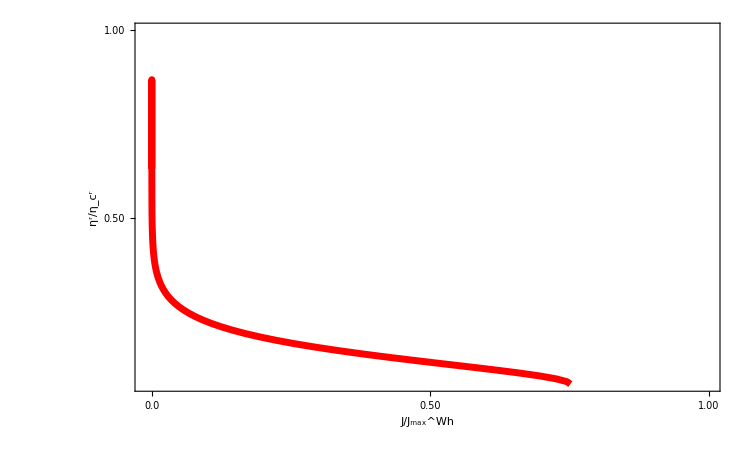

```mathematica
data4=Import["check80.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A4=ListLinePlot[{data4},Frame->True,PlotRange->{{-0.01,1},{0.06,1}},Frame->True,FrameTicks->{{{{-0.01,"0.0"},{1,"1.00"},{0.50,"0.50"}},None},{{{0,"0.0"},{1,"1.00"},{0.5,"0.50"}},None}},FrameLabel->{Style["J/J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(d).pdf",A4,ImageResolution->300]
```

/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(d).pdf

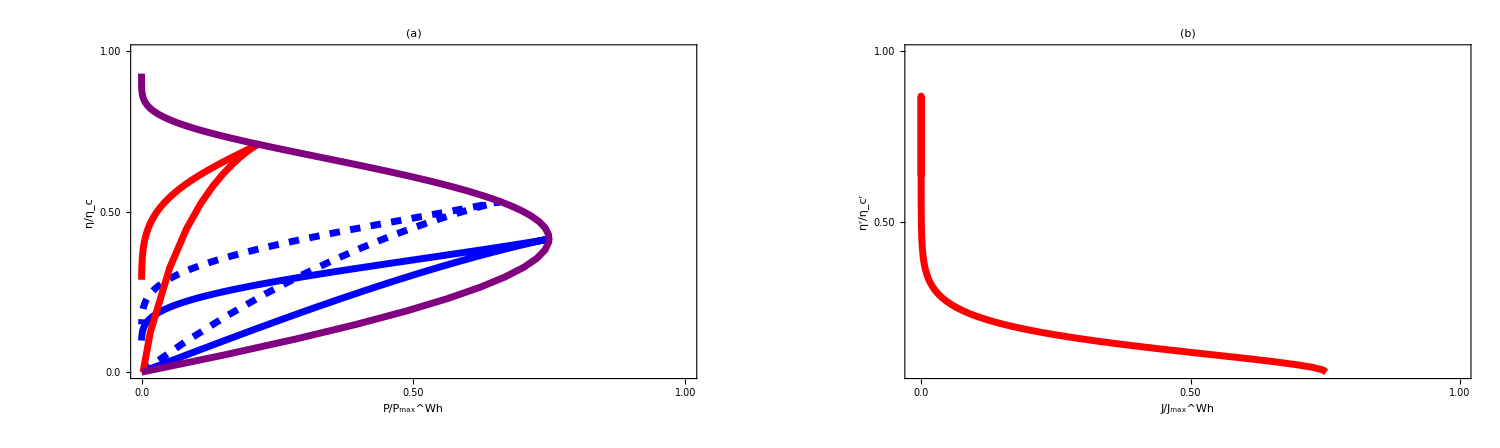

```mathematica
A5=GraphicsGrid[{{A1,A2}},ImageSize->1500]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig5.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig5.pdf

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
T3=1;
V=2Vg;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GaussKronrodRule",MaxRecursion->1000,AccuracyGoal->20];
I4=FindRoot[{I3[V3]==0},{{V3,Vg}}];
V3=V3/.I4[[1]];
I1=(2ec)/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,P/(2*0.316493),2*η}];
},{Vg,0,10,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check11.dat",list]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig10supple.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig10supple.pdf

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=2*2.52;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=2Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=(2ec)/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,T3,P/(2*0.316493),2*η}];
},{Vg,1,10,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check122.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.42811×10^-17 and 3.67673×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.24675×10^-15 and 1.28879×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.54813×10^-15 and 3.12397×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.35101×10^-13 and 2.49853×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.35101×10^-13 and 2.49853×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.90613×10^-17 and 1.98862×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.28585×10^-14 and 4.98225×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.45672×10^-13 and 3.35258×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.99302×10^-13 and 9.25279×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.99302×10^-13 and 9.25279×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.4729×10^-17 and 8.02914×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.36956×10^-13 and 5.59732×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.60276×10^-13 and 4.95829×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.77747×10^-12 and 3.95579×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.0744×10^-17 and 5.40009×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.58167×10^-16 and 4.52791×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.61986×10^-16 and 1.2879×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.81822×10^-18 and 3.28276×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.67662×10^-17 and 1.07022×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.6084×10^-16 and 1.15463×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.16584×10^-17 and 1.69024×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.48761×10^-18 and 1.48787×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.92901×10^-17 and 1.6023×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.41935×10^-18 and 1.17649×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{86.0566,Null}

check122.dat

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T12uu=TX TY;
T13uu=TX (1-TY);
T21uu=0;
T22uu=(1-TY);
T23uu=TY;
T31uu=TX;
T32uu=TY(1-TX);
T33uu=(1-TX)( 1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(1-T11uu)*G0*df,{G,n0,n1}];
G12=NIntegrate[(-T12uu)*G0*df,{G,n0,n1}];
G13=NIntegrate[(-T13uu)*G0*df,{G,n0,n1}];
G31=NIntegrate[(-T31uu)*G0*df,{G,n0,n1}];
G32=NIntegrate[(-T32uu)*G0*df,{G,n0,n1}];
G33=NIntegrate[(1-T33uu)*G0*df,{G,n0,n1}];
L11=NIntegrate[(1-T11uu)*(G-μ)*L0*df,{G,n0,n1}];
L12=NIntegrate[(-T12uu)*(G-μ)*L0*df,{G,n0,n1}];
L13=NIntegrate[(-T13uu)*(G-μ)*L0*df,{G,n0,n1}];
L23=NIntegrate[(-T23uu)*(G-μ)*L0*df,{G,n0,n1}];
L33=NIntegrate[(1-T33uu)*(G-μ)*L0*df,{G,n0,n1}];
L31=NIntegrate[(-T31uu)*(G-μ)*L0*df,{G,n0,n1}];
L32=NIntegrate[(-T32uu)*(G-μ)*L0*df,{G,n0,n1}];
π11=NIntegrate[(1-T11uu)*(G-μ)*Lp*df,{G,n0,n1}];
π12=NIntegrate[(-T12uu)*(G-μ)*Lp*df,{G,n0,n1}];
π13=NIntegrate[(-T13uu)*(G-μ)*Lp*df,{G,n0,n1}];
π31=NIntegrate[(-T31uu)*(G-μ)*Lp*df,{G,n0,n1}];
π33=NIntegrate[(1-T33uu)*(G-μ)*Lp*df,{G,n0,n1}];
K11=NIntegrate[(1-T11uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K12=NIntegrate[(-T12uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K13=NIntegrate[(-T13uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K31=NIntegrate[(-T31uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K32=NIntegrate[(-T32uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K33=NIntegrate[(1-T33uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
list=AppendTo[list1,{x1,T*Sc/Pc}];
},{x1,0,80,1}];//AbsoluteTiming
list=Sort[list1];
Export["check200.dat",list]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained 0.0000167091 and 2.35535×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained -0.0000164417 and 4.06804×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained -2.6744×10^-7 and 6.26319×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {0.406624}. NIntegrate obtained 1.26213×10^-19 and 4.41453×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {0.406624}. NIntegrate obtained 1.26213×10^-19 and 4.41453×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {0.406624}. NIntegrate obtained 1.26213×10^-19 and 4.41453×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.735}. NIntegrate obtained 7.62067×10^-10 and 2.04458×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.951}. NIntegrate obtained -7.46499×10^-10 and 7.64737×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.735}. NIntegrate obtained -1.05974×10^-11 and 7.42024×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {30.8935}. NIntegrate obtained 3.44392×10^-14 and 1.66793×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {30.8935}. NIntegrate obtained -3.38911×10^-14 and 2.26549×10^-18 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {30.8935}. NIntegrate obtained -3.44392×10^-14 and 1.66793×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {40.8602}. NIntegrate obtained 1.56379×10^-18 and 8.9162×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {40.8602}. NIntegrate obtained -1.53926×10^-18 and 4.1024×10^-21 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {40.8602}. NIntegrate obtained -1.56379×10^-18 and 8.9162×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {50.5294}. NIntegrate obtained 7.09848×10^-23 and 4.45247×10^-26 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {50.5294}. NIntegrate obtained -6.9853×10^-23 and 1.16436×10^-25 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.00006}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {60.6392}. NIntegrate obtained 3.20283×10^-27 and 1.09522×10^-28 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {60.6392}. NIntegrate obtained -3.16484×10^-27 and 1.36423×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {70.5393}. NIntegrate obtained 1.4393×10^-31 and 6.28127×10^-33 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {70.5393}. NIntegrate obtained -1.41686×10^-31 and 8.45717×10^-33 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {70.5393}. NIntegrate obtained -1.4393×10^-31 and 6.28127×10^-33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {60.6392}. NIntegrate obtained -3.20283×10^-27 and 1.09522×10^-28 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{28.1904,Null}

check200.dat

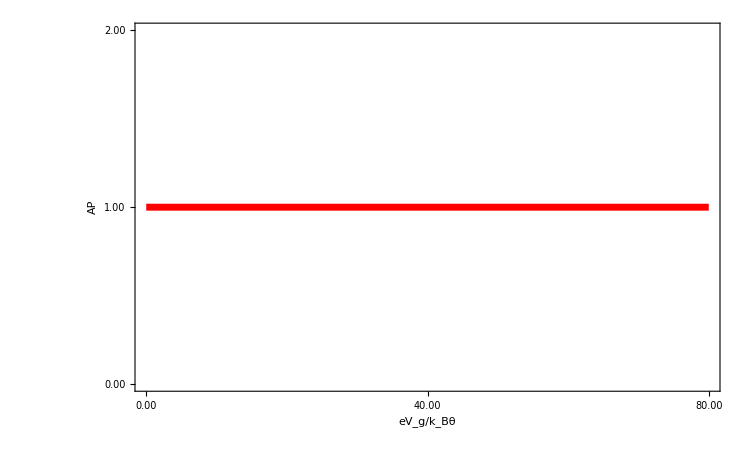

```mathematica
data4=Import["check200.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
A4=ListLinePlot[{data4},Frame->True,PlotRange->{{0,80},{0.0,2.00}},Frame->True,FrameTicks->{{{{0.00,"0.00"},{1.0,"1.00"},{2.0,"2.00"}},None},{{{0,"0.00"},{40,"40.00"},{80,"80.00"}},None}},FrameLabel->{Style["eV_g/k_Bθ",45,Bold,Black],Style["AP",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig3supple.pdf",A4,ImageResolution->300]
```

/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig3supple.pdf